# ALLENAMENTO

```mathematica
SetDirectory[NotebookDirectory[]];
Framed[ButtonBar[{"Integrali Definiti" :> NotebookLocate["slide2"], "Integrali Indefiniti" :> NotebookLocate["slide23"],
 "Integrali Misti" :>  NotebookLocate["slide44"]}, ImageSize -> {300, 100}, Alignment->Center,
  BaseStyle->{Orange, 22,
  Italic, Bold, FontFamily->"Times"}], Alignment->Center, RoundingRadius->5]
```

Integrali Definiti | Integrali Indefiniti | Integrali Misti

```mathematica
Framed[Tooltip[ButtonBar[{"Il mio integrale" :> NotebookLocate["IlMioIntegrale"]}, ImageSize->{300, 100},
 Alignment->Center, BaseStyle->{Orange, 22, Italic, Bold, FontFamily->"Times"}], "Calcola il tuo integrale!"],
  Alignment->Center, RoundingRadius->5]
```

Il mio integrale

## Integrali Definiti

```mathematica
Framed[ButtonBar[{"Scomposizione":> NotebookLocate["slide3"], "Sostituzione":> NotebookLocate["slide8"]}, 
ImageSize -> {300, 100}, Alignment->Center,
  BaseStyle->{Orange, 22,
  Italic, Bold, FontFamily->"Times"}]
  ButtonBar[{"Per parti":> NotebookLocate["slide13"], "Funzioni Razionali":> NotebookLocate["slide18"]}, 
ImageSize -> {300, 100}, Alignment->Center,
  BaseStyle->{Orange, 22,
  Italic, Bold, FontFamily->"Times"}], Alignment->Center, RoundingRadius->5]
```

Per parti | Funzioni Razionali Scomposizione | Sostituzione

```mathematica
Tooltip[Framed[Button[-Graphics-, ButtonData->NotebookLocate["Home"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->100, Alignment->Baseline], 
 "Torna alla Home"]
```

-Graphics-

## Integrali per scomposizione ■□□□□

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{5} x-2 \,dx", Magnification->5]
```

-Graphics-

```mathematica
Grid[{{Framed[Tooltip[ButtonBar[{"Soluzione" :> MessageDialog["\t\t\tLa soluzione e`:\n" Framed[StandardForm[5/2], BaseStyle-> 24, ImageSize->{315, 80}, FrameStyle->Red, RoundingRadius->10, Alignment->Center]]},
 ImageSize->{300, 100},
 Alignment->Center, BaseStyle->{Orange, 22, Italic, Bold, FontFamily->"Times"}], "Fammi vedere la soluzione!"],
  Alignment->Center, RoundingRadius->5], "               "Framed[Tooltip[ButtonBar[{"Soluzione guidata" :> MessageDialog["La soluzione e`:" StandardForm[5/2]]}, ImageSize->{300, 100},
 Alignment->Center, BaseStyle->{Orange, 22, Italic, Bold, FontFamily->"Times"}], "Fammi vedere i passi!"],
  Alignment->Center, RoundingRadius->5]}}]
```

Soluzione |                 Soluzione guidata

```mathematica
(* teoria, home, avanti *)
Framed[Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefScomp"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide4"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->320, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Integrali per scomposizione ■■□□□

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{4}  2x \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
(* teoria, home, avanti, indietro *)
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide3"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefScomp"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide5"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per scomposizione ■■■□□

```mathematica
<<MaTeX`
MaTeX[" \\int_{-2}^{-1}  3x^2-3  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide4"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefScomp"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide6"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per scomposizione ■■■■□

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{2}  2x+\\frac{2}{x}+e^x  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
(* teoria, home, avanti, indietro *)
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide5"];]
Button[-Graphics-,NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefScomp"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide7"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per scomposizione ■■■■■

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{4}  \\frac{1}{\\sqrt{x}}+\\frac{1}{x}+\\frac{1}{x^2}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
(* teoria, home, avanti, indietro *)
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide6"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefScomp"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide8"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■□□□□

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{e}  \\frac{\\ln(x)}{x} \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide7"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodoDefSostituzione"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide9"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■■□□□

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{1}  \\frac{e^x}{e^x+1}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide8"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodoDefSostituzione"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide10"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■■■□□

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{4}  \\frac{1}{\\sqrt{x}+x\\sqrt{x}}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide9"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodoDefSostituzione"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide11"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■■■■□

```mathematica
<<MaTeX`
MaTeX["\\int_{e}^{e^2}  \\frac{1}{x\\ln^2(x)}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide10"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodoDefSostituzione"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide12"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■■■■■

```mathematica
<<MaTeX`
MaTeX["\\int_{e-1}^{e^2-1}  \\frac{1}{(x+1)\\ln(x+1)}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide11"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodoDefSostituzione"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide13"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■□□□□

```mathematica
<<MaTeX`
MaTeX["\\int_{5}^{6}  5xe^x  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(* Inserire bottoni, soluzione e step by step*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide12"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefParti"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide14"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■■□□□

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{e}  \\frac{\\ln(x^2)}{x^2}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide13"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefParti"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide15"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■■■□□

```mathematica
<<MaTeX`
MaTeX["\\int_{-1}^{0} (x^2+x)e^{-x}\,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide14"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefParti"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide16"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■■■■□

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{3}  x^2\\ln(x)\,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide15"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefParti"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide17"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■■■■■

```mathematica
<<MaTeX`
MaTeX["\\int_{\\frac{\\pi}{2}}^{\\frac{3}{2}\\pi} x|\\sin(x)|\,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide16"];]
Button[-Graphics-, NotebookOpen["Project.nb"];NotebookLocate[{"Project.nb", "MetodiDefParti"}]] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide18"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■□□□□

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{\\frac{1}{3}} \\frac{1}{1+9x^2} \,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide17"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide19"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■■□□□

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{1}  \\frac{x-1}{x^2-4}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide18"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide20"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■■■□□

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{3}  \\frac{2x}{1+x^2}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide19"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide21"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■■■■□

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{2}  \\frac{x^5-x+1}{x^4+x^2}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide20"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide22"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■■■■■

```mathematica
<<MaTeX`
MaTeX["\\int_ {-2}^{-1} \\frac {x^4} {x - 1}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide21"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->320, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Integrali Indefiniti

```mathematica
Framed[ButtonBar[{"Scomposizione":> NotebookLocate["slide24"], "Sostituzione":> NotebookLocate["slide29"],
"Per parti":> NotebookLocate["slide34"], "Funzioni Razionali":> NotebookLocate["slide39"]}, 
ImageSize -> {300, 100}, Alignment->Center,
  BaseStyle->{Orange, 22,
  Italic, Bold, FontFamily->"Times"}], Alignment->Center, RoundingRadius->5]
```

Scomposizione | Sostituzione | Per parti | Funzioni Razionali

```mathematica
Tooltip[Framed[Button[-Graphics-, ButtonData->NotebookLocate["Home"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->100, Alignment->Baseline], 
 "Torna alla Home"]
```

-Graphics-

## Integrali per scomposizione ■□□□□

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{x^3}{2}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide25"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->320, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Integrali per scomposizione ■■□□□

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{7\\cos(x)}{8} \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide24"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide26"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per scomposizione ■■■□□

```mathematica
<<MaTeX`
MaTeX["\\int  x^5+5x^4+\\frac{x^3}{3}+3x^2+1  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide25"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide27"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per scomposizione ■■■■□

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{2}{x}+1   \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide26"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide28"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per scomposizione ■■■■■

```mathematica
<<MaTeX`
MaTeX["\\int  3e^x+5x  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Buttoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide27"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide29"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■□□□□

```mathematica
<<MaTeX`
MaTeX["\\int  \\frac{e^x}{e^{2x}+1} \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Buttoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide28"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide30"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■■□□□

```mathematica
<<MaTeX`
MaTeX["\\int  \\frac{\\ln(x)}{x(\\ln^4(x)+1)} \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide229"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide31"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■■■□□

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{e^{2x}+3e^x}{e^x+1}  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide30"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide32"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■■■■□

```mathematica
<<MaTeX`
MaTeX["\\int \\cos(x)\\sin(x)  \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide31"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide33"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per sostituzione ■■■■■

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{\\sin(1+\\sqrt{x})}{\\sqrt{x}} \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide32"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide34"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■□□□□

```mathematica
<<MaTeX`
MaTeX["\\int  xe^x \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide33"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide35"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■■□□□

```mathematica
<<MaTeX`
MaTeX["\\int  \\frac{\\ln(x)}{x^4} \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide34"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide36"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■■■□□

```mathematica
<<MaTeX`
MaTeX["\\int  2x\\arctan(x) \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide35"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide37"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■■■■□

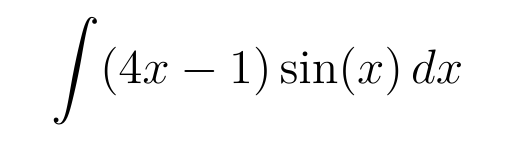

```mathematica
<<MaTeX`
MaTeX["\\int (4x-1)\\sin(x)  \,dx", Magnification->5]
```

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide36"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide38"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali per parti ■■■■■

```mathematica
<<MaTeX`
MaTeX["\\int \\ln^2(x) \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide37"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide39"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■□□□□

```mathematica
<<MaTeX`
MaTeX["\\int  \\frac{x+1}{x-3}    \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide38"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide40"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■■□□□

```mathematica
<<MaTeX`
MaTeX["\\int  \\frac{x-x^2}{1+x}    \,dx", Magnification->5]
```

-Graphics-

```mathematica
(*Bottoni*)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide39"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide41"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■■■□□

```mathematica
<<MaTeX`
MaTeX["\\int  \\frac{1}{9+4x^2}    \,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide40"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide42"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■■■■□

```mathematica
<<MaTeX`
MaTeX["\\int  \\frac{2x^2+4}{x^2+x+1}    \,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide41"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];] Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide43"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->430, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Integrali di funzioni razionali ■■■■■

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{3x+1}{x^3+2x^2+x+2}    \,dx", Magnification->5]
```

-Graphics-

```mathematica
(**)
```

```mathematica
Framed[Button[ImageRotate[-Graphics-], ButtonData->NotebookLocate["slide42"];]Button[-Graphics-, ButtonData->NotebookLocate["Teoria"];] Button[-Graphics-, ButtonData->NotebookLocate["Home"];],
 FrameStyle->Directive[Orange, 82], RoundingRadius->10, ImageSize->320, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Integrali Misti